```mathematica
Reϵ[ω_, ω0_, γ_] = 1 + (ω0^2 - ω^2)/((ω0^2 - ω^2)^2 + ω^2  γ^2)
```

1+(-ω^2+ω0^2)/(γ^2 ω^2+(-ω^2+ω0^2)^2)

```mathematica
Imϵ[ω_, ω0_, γ_] = (ω γ)/((ω0^2 - ω^2)^2 + ω^2  γ^2)
```

(γ ω)/(γ^2 ω^2+(-ω^2+ω0^2)^2)

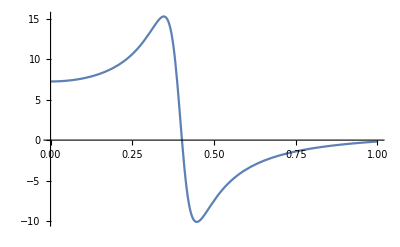
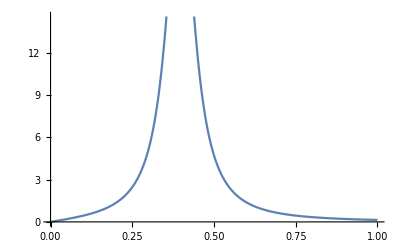

```mathematica
{Plot[Reϵ[ω, 0.4, 0.1], {ω, 0, 1}], Plot[Imϵ[ω, 0.4, 0.1], {ω, 0, 1}]}
```

```mathematica
L = 50;
ϵ = 0.00001;
ω0 = 0.5 ;
γ = 0.1 ;
```

```mathematica
{Re[N[(- 1)/π∫_-L^L (Imϵ[ν, ω0, γ]/(ω - ν + ⅈ ϵ) /. ω -> 0.2) ⅆν ]], Reϵ[0.2, ω0, γ] - 1}
```

{4.71891,4.7191}

```mathematica
{Re[N[1/π∫_-L^L ((Reϵ[ν, ω0, γ]-1)/(ω - ν + ⅈ ϵ) /. ω -> 0.1) ⅆν ]], Imϵ[0.1, ω0, γ] }
```

{0.173331,0.17331}

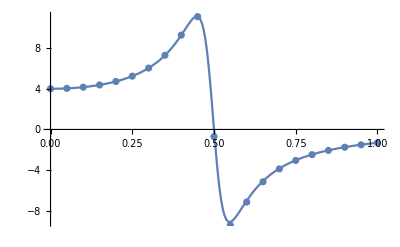

```mathematica
Show[Plot[Reϵ[ω, ω0, γ] - 1, {ω, 0, 1}], ListPlot[Table[{ω, Re[N[(- 1)/π∫_-L^L (Imϵ[ν, ω0, γ]/(ω - ν + ⅈ ϵ) ) ⅆν ]]}, {ω, 0.0, 1.0, 0.05}]]]
```

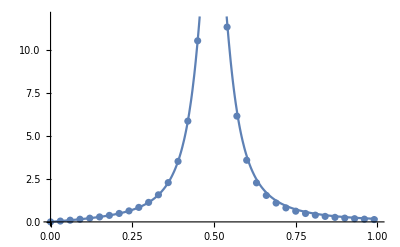

```mathematica
Show[Plot[Imϵ[ω, ω0, γ] , {ω, 0, 1}], ListPlot[Table[{ω, Re[N[1/π∫_-L^L ((Reϵ[ν, ω0, γ]-1)/(ω - ν + ⅈ ϵ) ) ⅆν ]]}, {ω, 0.0, 1.0, 0.03}]]]
```

```mathematica
Manipulate[Which[Part == "Re", Show[Plot[Reϵ[ω, ω0, γ] - 1, {ω, 0, 1}], ListPlot[Table[{ω, Re[N[(- 1)/π∫_-L^L (Imϵ[ν, ω0, γ]/(ω - ν + ⅈ ϵ) ) ⅆν ]]}, {ω, 0.0, 1.0, 0.05}]]], Part=="Im", Show[Plot[Imϵ[ω, ω0, γ] , {ω, 0, 1}], ListPlot[Table[{ω, Re[N[1/π∫_-L^L ((Reϵ[ν, ω0, γ]-1)/(ω - ν + ⅈ ϵ) ) ⅆν ]]}, {ω, 0.0, 1.0, Δω}]]]], {{L, 20}, 10, 60},{{ω0, 0.5}, 0, 1}, {{Δω, 0.02}, 0.001, 0.5},{Part, {"Re", "Im"}}]
```